## Meta-settings

```mathematica
$Version
```

12.2.0 for Microsoft Windows (64-bit) (February 1, 2021)

```mathematica
Charting`ResolvePlotTheme[Automatic,VectorPlot];
vcf=ColorDataFunction[…];
```

```mathematica
Monitor`NestList[f_,init_,n_]:=Module[{it=0},PrintTemporary[ProgressIndicator[Dynamic[it/n]]];
NestList[(it++;f[#])&,init,n]]
(*WFQTransit[weights_List,relaxation_:0]:=Function[state,RandomChoice[weights:>((#+state)&/@(IdentityMatrix[Length]~Join~(-IdentityMatrix[Length[state]])))]]*)
```

```mathematica
SetOptions[SelectedNotebook[],PrintingStyleEnvironment->"Printout",ShowSyntaxStyles->True]
```

### Test for Изжо Лю

```mathematica
n=4;
Normal@SparseArray[{{i_,j_}/;j>i:>ⅇ^(-ⅈ*π/4)},{n,n}];
mat=%+%†+IdentityMatrix[n];
Clear[n]
mat//MatrixForm
PositiveSemidefiniteMatrixQ@mat
```

(1 | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | 1 | ⅇ^(-(ⅈ π)/4) | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | 1 | ⅇ^(-(ⅈ π)/4)
ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | ⅇ^((ⅈ π)/4) | 1)

False

## Soft transitter

### Basic Idea

```mathematica
ComplexPlot3D[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z)),{z,0*(1+ ⅈ),2ⅇ*(1+ ⅈ)},ColorFunction->(Hue[2.95*(#8+0.5)]&),PlotLegends->BarLegend["Rainbow"],PlotRange->All,Mesh->Full]
```

-Graphics3D-

```mathematica
Simplify[(1+ⅇ^(-Im@z))(1-ⅇ^(-Re@z))+ⅈ(1+ⅇ^(-Re@z))(1-ⅇ^(-Im@z))/.z->(a+ⅈ b)]/.{Im[a]->0,Im[b]->0,Re[a]->a,Re[b]->b,Re[a+b]->a+b}
%//Expand
```

(1+ⅈ) ⅇ^(-a-b) (-1-ⅈ ⅇ^a+ⅈ ⅇ^b+ⅇ^(a+b))

(1+ⅈ)-(1-ⅈ) ⅇ^-a-(1+ⅈ) ⅇ^(-a-b)+(1-ⅈ) ⅇ^-b

### Visualization of the softness

```mathematica
Manipulate[VectorPlot[-{(1-ⅇ^(-x/n0))(1+ⅇ^(-y/n0)),(1+ⅇ^(-x/n0))(1-ⅇ^(-y/n0))},{x,0,5},{y,0,5}, VectorPoints->Tuples[Range[0,5],2],VectorMarkers->"Drop",VectorScaling->Automatic,VectorRange->All,VectorColorFunction->(vcf[#5/2]&),VectorColorFunctionScaling->False,PlotLegends->BarLegend[{(vcf[#/2]&),{0,2}}],Epilog->{vcf[0],Point[{0,0}]}],{{n0,1},0.1,20}]
```

```mathematica
Manipulate[VectorPlot3D[-{(1+ⅇ^(-y/n0)+ⅇ^(-z/n0))(1-ⅇ^(-x/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-z/n0))(1-ⅇ^(-y/n0)),(1+ⅇ^(-x/n0)+ⅇ^(-y/n0))(1-ⅇ^(-z/n0))},{x,0,3},{y,0,3},{z,0,3}, VectorPoints->Tuples[Range[0,3],3]],{{n0,1},0.0001,5}]
```

## Time-regime simulation

```mathematica
maxstep=50000;
```

### Verification of Convergence

```mathematica
Transit[n_,n0_:1]:=RandomChoice[{1,2(1-ⅇ^(-n/n0))}:>{n+1,n-1}]
myhist[ls_]:=BarChart[MeanAround/@(Transpose@PadRight[(HistogramList/@Partition[ls,Floor[Sqrt[Length[ls]]]])⟦All,2⟧,Automatic,""]/.""->Nothing),BarSpacing->None]
```

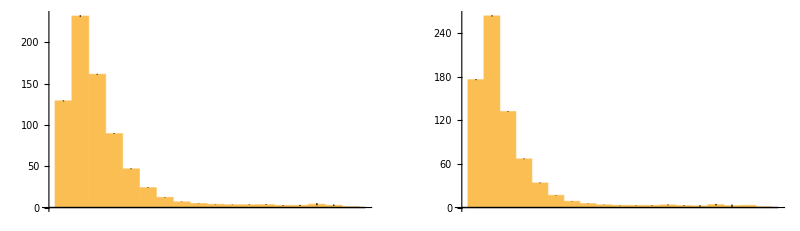

```mathematica
ls1=@NestList[Transit[#,1]&,0,maxstep]//Quiet;
ls0=@NestList[Transit[#,0.001]&,0,maxstep]//Quiet;
GraphicsRow[{myhist[ls1],myhist[ls0]}]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=Monitor`NestList[Transit[#,1]&,{0,0},maxstep]//Quiet;
```

### Simulations

#### Softened

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1-ⅇ^(-n1/n0))(1+ⅇ^(-n2/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=@NestList[Transit[#,1]&,{0,0},maxstep]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,(1+ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),(1+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=@NestList[Transit[#,0.01]&,{0,0},maxstep]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls11=@NestList[Transit[#,1]&,{0,0},10]//Quiet;
Histogram3D[ls11,ColorFunction->"TemperatureMap"]
```

Histogram3D::ldata: nestListWithMonitor[Transit[#1,1]&,{0,0},10] is not a valid dataset or list of datasets.

Histogram3D[nestListWithMonitor[Transit[#1,1]&,{0,0},10],ColorFunction→TemperatureMap]

```mathematica
Transit[{n1_,n2_},n0_:1]:=RandomChoice[{1/2,1/2,2/11(1+10 ⅇ^(-n2/n0))(1-ⅇ^(-n1/n0)),2/11(10+ⅇ^(-n1/n0))(1-ⅇ^(-n2/n0))}:>{{n1+1,n2},{n1,n2+1},{n1-1,n2},{n1,n2-1}}]
ls00=@NestList[Transit[#,0.01]&,{0,0},maxstep]//Quiet;
Histogram3D[ls00,ColorFunction->"TemperatureMap"]
```

-Graphics3D-

Binomial - Poisson entropic inequalities and the M/M/∞ queueBinomial - Poisson entropic inequalities and the M/M/∞ queue

```mathematica
RandomReal[]
```

0.170129

#### Generic

```mathematica
WFQTransitGenerate[λ_,μ_,Δt_,p_,w_]:=With[{K=Length[p]},Function[n,Module[{W,Wsum},
W=Function[m,Table[If[Indexed[m,k]==0,0,w⟦k⟧],{k,1,K}]];Wsum=Function[m,Sum[If[Indexed[m,k]==0,0,w⟦k⟧],{k,1,K}]];
Table[Indexed[n,k],{k,1,K}]+
RandomChoice[N[Exp[Δt λ p]~Join~Exp[Δt μ W[n] If[Wsum[n]==0,0,1/Wsum[n]]]-1]:>Evaluate@Catenate@{IdentityMatrix[K],-IdentityMatrix[K]}]
]]]
```

Exploration

```mathematica
ρ=.9;K=1;Δt=0.01;t=10;
μ=1;λ=μ ρ;maxstep=Round[t/Δt];size=6;
func=WFQTransitGenerate[λ,μ,Δt,Table[1./K,K],Table[1./K,K]];
ls11=@NestList[func,Table[0,K],10^size]//Quiet;
ls11MnStd=@Table[{Mean[#],If[Length[#]>1,StandardDeviation[#],Nothing]}&@(Moment[#,r UnitVector[K,1]]&/@Partition[N@ls11,length]),{length,Evaluate@Table[10^k,{k,1,size}]},{r,0,5}];
```

```mathematica
ls11MnArn=@Map[Around[#⟦1⟧,If[NumberQ[#⟦2⟧]&&(#⟦2⟧>0),{Min[#⟦1⟧-10^-5,#⟦2⟧],#⟦2⟧},10^-10]]&,Most[ls11MnStd],{2}]~Join~{Flatten[Last[ls11MnStd]]};
ls11MnRel=(#/Last[ls11MnArn])&/@Most[ls11MnArn];
```

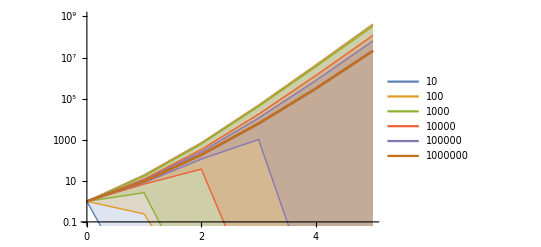

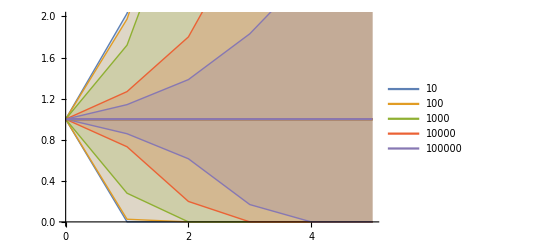

```mathematica
ListLogPlot[ls11MnArn,PlotRange->{.1,1×10^9},Joined->True,IntervalMarkers->"Bands",PlotLegends->Table[10^k,{k,1,size}],Ticks->{Range[0,5],Automatic},DataRange->{0,5}]
ListPlot[ls11MnRel,PlotRange->{Automatic,{1.0,All}},Joined->True,IntervalMarkers->"Bands",PlotLegends->Table[10^k,{k,1,size}],Ticks->{Range[0,5],Automatic},DataRange->{0,5}]
```

```mathematica
Needs["ComputerArithmetic`"]
Map[Flatten,Map[If[Length[#]==1,Append[#,NaN],#]&,ls11MnStd,{2}],{1,2}]
SetDirectory["C:\\Users\\Fang Tci\\Desktop"]
Export["ls11MnArn.xlsx",%%/.NaN->"=1/0"]
```

{{1.,0.,9.45857,9.73935,185.81,520.892,6089.56,41673.9,307066.,3.9779×10^6,2.12649×10^7,4.01987×10^8},{1.,0.,9.45857,9.21487,185.81,510.397,6089.56,41128.3,307066.,3.91645×10^6,2.12649×10^7,3.93487×10^8},{1.,0.,9.45857,6.81698,185.81,431.54,6089.56,35094.7,307066.,3.22866×10^6,2.12649×10^7,3.12381×10^8},{1.,0.,9.45857,2.53956,185.81,148.818,6089.56,11393.,307066.,1.02453×10^6,2.12649×10^7,9.84336×10^7},{1.,0.,9.45857,1.33977,185.81,71.6026,6089.56,5062.19,307066.,445729.,2.12649×10^7,4.29006×10^7},{1.,NaN,9.45857,NaN,185.81,NaN,6089.56,NaN,307066.,NaN,2.12649×10^7,NaN}}

C:\Users\Fang Tci\Desktop

ls11MnArn.xlsx

Turn into a function

```mathematica
Needs["ComputerArithmetic`"]
ql11MnStd[K_,ρ_:.9,μ_:1,Δt_:.01,magn_:6,maxr_:5]:=Module[
{(*K=1,ρ=.9,*)λ,(*μ=1,Δt=0.01,magn=6,maxr=5,*)
func,ql11,ql11Time,ql11MnStd,ql11MnTime(*,ql11MnArn,ql11MnRel*)},λ=μ ρ;

func=WFQTransitGenerate[λ,μ,Δt,Table[1./K,K],Table[1./K,K]];
{ql11Time,ql11}=Timing@[NestList[func,Table[0,K],10^magn],"Label"->StringTemplate["Simulation\n`1`"][<|"K"->K,"λ"->λ,"μ"->μ,"Δt"->Δt|>]]//Quiet;
{ql11MnTime,ql11MnStd}=Timing@[Table[{Mean[#],If[Length[#]>1,StandardDeviation[#],Nothing]}&@(Moment[#,r UnitVector[K,1]]&/@Partition[N@ql11,length]),{length,Evaluate@Table[10^k,{k,1,magn}]},{r,0,maxr}],"Label"->StringTemplate["Calculating mean and STD\n`1`"][<|"magn"->magn,"maxr"->maxr|>]];
<|"SimulationTime"->ql11Time,"SimulationTrace"->ql11,"StatisticsTime"->ql11MnTime,"Statistics"->ql11MnStd|>
(*
ql11MnArn=@Map[Around[#⟦1⟧,If[NumberQ[#⟦2⟧]&&(#⟦2⟧>0),{Min[#⟦1⟧-10^-5,#⟦2⟧],#⟦2⟧},10^-10]]&,Most[ql11MnStd],{2}]~Join~{Flatten[Last[ql11MnStd]]};
ql11MnRel=(#/Last[ql11MnArn])&/@Most[ql11MnArn];
*)
]
```

Script to run

```mathematica
$Version
```

12.2.0 for Linux x86 (64-bit) (January 7, 2021)

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop"}]]
Module[{filename="ql11MnStd.xlsx",K=8,ρ=.9,μ=1,Δt=0.01,magn=8,maxr=10,res,timing,calctime,array,stringargs},
Export[filename,[ParallelTable[["SetCurrent"][StringTemplate["K=`1`"][K]];res=ql11MnStd[K,ρ,μ,Δt,magn,maxr];{timing,calctime,array}=Values[res⟦{"SimulationTime","StatisticsTime","Statistics"}⟧];stringargs=Sequence[K,ρ,μ,Δt,magn,maxr,timing,calctime];StringTemplate["K`1`"][stringargs]->ArrayFlatten[({{{{StringTemplate["(`7`s`8`s)ρ`2`μ`3`Δt`4`"][stringargs]}}, {Flatten@Table[{r,"STD"},{r,0,maxr}]}}, {{Table[10^k,{k,1,magn}]}ᵀ, Map[Flatten,Map[If[Length[#]==1,Append[#,NaN],#]&,array,{2}],{1,2}]}})],{K,1,K}],"Label"->StringTemplate["M/M/1-FQ MC\nK≤`1`, ρ=`2`, μ=`3`, Δt=`4`,\nsteps≤10^(`5`), r≤`6`"][K,ρ,μ,Δt,magn,maxr]]]]//Quiet
```

Plotting

```mathematica
ql11MnStdXlsx=(Import[FileNameJoin[{$HomeDirectory,"Desktop","ql11MnStd.xlsx"}]]/."NaN"->NaN);
```

```mathematica
ql11plots=@Table[K=4i+j;Module[{tag=ql11MnStdXlsx⟦K,1,1⟧,magn=Round[Log10[ql11MnStdXlsx⟦K,-1,1⟧]],maxr=ql11MnStdXlsx⟦K,1,-2⟧,ls11MnStd=(Partition[#,2]&/@ql11MnStdXlsx⟦K,2;;,2;;⟧/.NaN->Nothing),ls11MnArn,ls11MnRel},
ls11MnArn=@Map[Around[#⟦1⟧,If[NumberQ[#⟦2⟧]&&(#⟦2⟧>0),{Min[#⟦1⟧-10^-10,#⟦2⟧],#⟦2⟧},10^-10]]&,Most[ls11MnStd],{2}]~Join~{Flatten[Last[ls11MnStd]]};
ls11MnRel=(#/Last[ls11MnArn])&/@Most[ls11MnArn];
Labeled[GraphicsRow[{
ListLogPlot[ls11MnArn,PlotRange->{{0,maxr},{.1,Max[ls11MnArn⟦1,-1⟧["Interval"]]}},Joined->True,Ticks->{Range[0,maxr],Automatic},DataRange->{0,maxr}],
ListPlot[ls11MnRel,PlotRange->{{0,maxr},{1.0,Max[ls11MnRel⟦1,-1⟧["Interval"]]}},Joined->True,IntervalMarkers->"Bands",Ticks->{Range[0,maxr],Automatic},DataRange->{0,maxr},AxesOrigin->{maxr,1}]
},Spacings->Scaled[.01]],StringTemplate["K=`1` `2`"][K,tag],Top]
],{j,1,4},{i,0,1}];
```

```mathematica
{{LineLegend[Array[ColorData[97],8],Table[StringTemplate["10^(`1`)"][k],{k,1,8}],LegendLabel->"Sample size"]},
Splice@Table[{SpanFromAbove},3]}
```

```mathematica
GraphicsRow[{
GraphicsGrid[ArrayFlatten[{{ql11plots}}],ImageSize->1200,Spacings->0],
LineLegend[Array[ColorData[97],8],Table[StringTemplate["10^(`1`)"][k],{k,1,8}],LegendLabel->"Sample size"]
},Spacings->0,ImageSize->1300]
```

#### Waiting-time computations

Utilities

```mathematica
func[r_,q_]:=(Expand@(Sum[Indexed[S,k],{k,1,q}]^r))/.{Indexed[S,_]^r_:>Indexed[s,r],Indexed[S,_]->s}//Expand
coeffunc[r_,k_]:=Module[{partitions=Reverse/@Reverse@IntegerPartitions[r,k],counts,ns},
counts=Counts/@partitions;ns=Total/@Values/@counts;
{partitions,Times@@{Binomial[k,#]&/@ns,(Multinomial@@#)&/@Values/@counts,(Multinomial@@#)&/@partitions}}ᵀ]
polyfunc[r_,k_]:=Module[{partitions,coefs},{partitions,coefs}=coeffunc[r,k]ᵀ;
coefs.(Product[If[r==1,s,Indexed[s,r]],{r,Evaluate@#}]&/@partitions)]
```

```mathematica
Table[func[r,q],{r,1,6},{q,1,4}]//TableForm
```

s | 2 s | 3 s | 4 s
s2 | 2 s^2+2 s2 | 6 s^2+3 s2 | 12 s^2+4 s2
s3 | 6 s s2+2 s3 | 6 s^3+18 s s2+3 s3 | 24 s^3+36 s s2+4 s3
s4 | 6 s2^2+8 s s3+2 s4 | 36 s^2 s2+18 s2^2+24 s s3+3 s4 | 24 s^4+144 s^2 s2+36 s2^2+48 s s3+4 s4
s5 | 20 s2 s3+10 s s4+2 s5 | 90 s s2^2+60 s^2 s3+60 s2 s3+30 s s4+3 s5 | 240 s^3 s2+360 s s2^2+240 s^2 s3+120 s2 s3+60 s s4+4 s5
s6 | 20 s3^2+30 s2 s4+12 s s5+2 s6 | 90 s2^3+360 s s2 s3+60 s3^2+90 s^2 s4+90 s2 s4+36 s s5+3 s6 | 1080 s^2 s2^2+360 s2^3+480 s^3 s3+1440 s s2 s3+120 s3^2+360 s^2 s4+180 s2 s4+72 s s5+4 s6

Simulation processing

```mathematica
SetDirectory[FileNameJoin[{$HomeDirectory,"Desktop"}]]
Module[{filename="ql11MnStd.xlsx",K=8,ρ=.9,μ=1,Δt=0.01,magn=8,maxr=10,res,timing,calctime,array,stringargs},
Export[filename,[ParallelTable[["SetCurrent"][StringTemplate["K=`1`"][K]];res=ql11MnStd[K,ρ,μ,Δt,magn,maxr];{timing,calctime,array}=Values[res⟦{"SimulationTime","StatisticsTime","Statistics"}⟧];stringargs=Sequence[K,ρ,μ,Δt,magn,maxr,timing,calctime];StringTemplate["K`1`"][stringargs]->ArrayFlatten[({{{{StringTemplate["(`7`s`8`s)ρ`2`μ`3`Δt`4`"][stringargs]}}, {Flatten@Table[{r,"STD"},{r,0,maxr}]}}, {{Table[10^k,{k,1,magn}]}ᵀ, Map[Flatten,Map[If[Length[#]==1,Append[#,NaN],#]&,array,{2}],{1,2}]}})],{K,1,K}],"Label"->StringTemplate["M/M/1-FQ MC\nK≤`1`, ρ=`2`, μ=`3`, Δt=`4`,\nsteps≤10^(`5`), r≤`6`"][K,ρ,μ,Δt,magn,maxr]]]]//Quiet
```

```mathematica
Table[ql11MnStd[1,ρ,1,0.01,5,4],{ρ,{.2,.4,.6,.8}}]
```

{<|SimulationTime→8.46875,SimulationTrace→{{0},{1},{0},{1},{0},{1},{0},{1},99985,{1},{0},{1},{0},{1},{0},{1},{2}},1,Statistics→{{{1.,0.},{0.7484,0.330993},{1.11724,1.13005},{2.12126,4.4282},{5.18128,20.7353}},3,{{1.},{0.7484},{1.11724},{2.12126},{5.18128}}}|>,2,<|1|>}
 |  |  |  |

```mathematica
Transpose/@Map[Around@@#&,(#⟦"Statistics"⟧&/@%18),{3}]
```

```mathematica
Transpose/@Map[#⟦-1⟧&,(#⟦"Statistics"⟧&/@%18),{3}]
```

{{{0.,0.,0.,0.,1.},{0.330993,0.114882,0.0429338,0.0133965,0.7484},{1.13005,0.406149,0.151078,0.0500074,1.11724},{4.4282,1.64937,0.588958,0.20313,2.12126},{20.7353,8.02707,2.70643,0.944078,5.18128}},{{0.,0.,0.,0.,1.},{0.78882,0.319947,0.0992302,0.0248016,1.16048},{4.43578,1.87259,0.598819,0.159936,2.67732},{31.4662,13.2486,4.62428,1.18471,8.70422},{275.799,113.704,43.3769,11.1411,38.1523}},{{0.,0.,0.,0.,1.},{1.77112,1.02867,0.350075,0.105694,2.00208},{17.6055,11.1307,4.05137,1.05197,8.15244},{217.375,137.731,51.9827,13.1254,50.1941},{3171.35,1919.76,735.097,191.954,422.076}},{{0.,0.,0.,0.,1.},{4.01592,3.20089,1.32842,0.434228,4.29482},{69.8687,58.2123,24.063,6.97336,35.8978},{1387.24,1151.6,463.518,131.043,427.982},{31659.5,25794.7,9960.93,2812.94,6402.89}}}

```mathematica
SetDirectory["C:\\Users\\Fang Tci\\Desktop"]
Export["temp.xlsx",%44]
```

C:\Users\Fang Tci\Desktop

temp.xlsx

```mathematica
Table[ql11MnStd[K,.6,1,0.01,5,4],{K,1,4}]
```

{<|SimulationTime→7.25,SimulationTrace→{{0},{1},{2},{1},{2},{1},{0},{1},{0},99983,{0},{1},{0},{1},{2},{1},{2},{3},{2}},…→2.07813,Statistics→{{{1.,0.},{1.99122,1.70504},{7.8766,16.0236},{45.9607,190.405},{362.854,2703.86}},3,{{1.},{1.99122},{7.8766},{45.9607},{362.854}}}|>,2,<|1|>}
 |  |  |  |

```mathematica
Transpose/@Map[#⟦-1⟧&,(#⟦"Statistics"⟧&/@%48),{3}]
```

{{{0.,0.,0.,0.,1.},{1.70504,0.993181,0.332801,0.114708,1.99122},{16.0236,10.6919,3.53584,1.4166,7.8766},{190.405,135.445,44.2563,18.7617,45.9607},{2703.86,1928.98,621.641,265.631,362.854}},{{0.,0.,0.,0.,1.},{1.17543,0.709026,0.274755,0.088906,1.04053},{8.05215,5.39449,2.17511,0.752518,2.97241},{76.5446,50.4266,20.2702,7.20878,13.1389},{869.167,538.397,210.595,75.2245,83.1492}},{{0.,0.,0.,0.,1.},{0.851588,0.461865,0.150879,0.0478076,0.66638},{3.99159,2.25389,0.719598,0.202194,1.50436},{24.6955,13.4896,4.25733,1.07378,4.94156},{183.922,95.9171,30.1695,7.20576,21.8594}},{{0.,0.,0.,0.,1.},{0.690534,0.348891,0.105994,0.0332345,0.51087},{2.6555,1.42053,0.44095,0.158996,0.98569},{14.0485,7.42234,2.34107,0.853374,2.67177},{88.4427,45.0054,14.28,5.07883,9.79477}}}

```mathematica
SetDirectory["C:\\Users\\Fang Tci\\Desktop"]
Export["temp.xlsx",%44]
```

C:\Users\Fang Tci\Desktop

temp.xlsx

## Correlation

### Copula

```mathematica
Plot3D[Min[x,y],{x,0,1},{y,0,1}]
```

-Graphics3D-

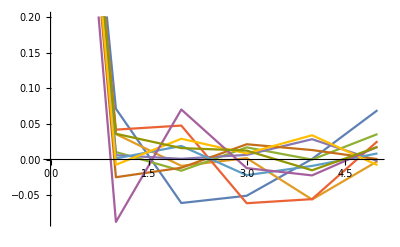

```mathematica
CorrelationFunction[#,{5}]&/@data//ListLinePlot
```

```mathematica
CorrelationFunction[BinomialProcess[p],s,t]
Flatten[Table[{s,t,Evaluate[%/.(p->2/3)]},{s,1,10},{t,1,10}],1];
Show[Plot3D[Evaluate[%%/.(p->2/3)],{s,1,10},{t,1,10},Exclusions->None],ListPointPlot3D[%]]
```

Min[s,t]/(√(s t))

-Graphics3D-

```mathematica
Max[Max[(w+x),0]+x2,0]//FullSimplify
```

Max[0,x2+Max[0,w+x]]

```mathematica
Reduce[Max[Max[(w+x),0]+x2,0]==0,x2]
```

Max[0,w+x]∈ℝ&&x2≤-Max[0,w+x]

```mathematica
DensityPlot3D[{Max[Max[w,0]+x,0]},{w,0,1},{x,-1,1},AxesLabel->Automatic,PlotLegends->Automatic,OpacityFunction->(Max[#,0]/4&),OpacityFunctionScaling->False]
```

```mathematica
Show[DensityPlot3D[{Max[Max[(w+x),0]+x2,0]},{w,0,1},{x,-1,0},{x2,-.5,.5},AxesLabel->{"w","x","x2"},PlotLegends->Automatic,OpacityFunction->(Max[#,0]/4&),OpacityFunctionScaling->False],
ContourPlot3D[{w+x+x2==0,w+x==0,x2==0},{w,0,1},{x,-1,0},{x2,-.5,5},ContourStyle->Opacity[0.1],RegionBoundaryStyle->None,RegionFunction->Function[{w,x,x2},(x2≥0&&Abs[w+x]<1*^-2)||(x2<-1*^-9&&w+x>1*^-2)||(w+x≤0&&Abs[x2]<1*^-2)]],
ParametricPlot3D[{w,-w,0},{w,0,1},PlotStyle->Black]]
```

-Graphics3D-

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\Fang Tci\Documents\吴昊-华为本研\ddr-wfq-sla-ml\q1rw

```mathematica
Export["Assets\\two-step-iteration.png",%26]
```

Assets\two-step-iteration.png

### Native Expressions

#### Native Example

```mathematica
ℋ=DiscreteMarkovProcess[{0.5,0.5},({{0.7, 0.3}, {0.25, 0.75}})];
ℋ//=ReplacePart[#,1->((#/Norm[#,1])&@Array[PDF[StationaryDistribution[#]],Length@MarkovProcessProperties[#,"TransitionMatrix"]])]&;
𝒜=HiddenMarkovProcess[ℋ,({{0.8, 0.2}, {0.6, 0.4}})];
```

#### MAP Example

```mathematica
𝒟0=({{-2, 0}, {0, -1/2}});𝒟1=({{3/5, 7/5}, {7/20, 3/20}});dt=1;
transitM=N@MatrixExp[dt (𝒟0+𝒟1)];
emitM=N@MatrixExp[dt 𝒟1];
ℋ=DiscreteMarkovProcess[{0.5,0.5},transitM];
ℋ//=ReplacePart[#,1->((#/Norm[#,1])&@Array[PDF[StationaryDistribution[#]],Length@MarkovProcessProperties[#,"TransitionMatrix"]])]&;
𝒜=HiddenMarkovProcess[ℋ,(#/Total/@#)&@𝒟1];
```

#### Strong Autocorrelation Example

```mathematica
ℋ=DiscreteMarkovProcess[1,({{0.05, 0.95, 0.00}, {0.00, 0.05, 0.95}, {0.95, 0.00, 0.05}})];
𝒜=HiddenMarkovProcess[ℋ,({{0.9, 0.1}, {0.1, 0.9}, {0.1, 0.9}})];
```

#### Poisson Example

```mathematica
𝒜=PoissonProcess[0.01];
```

#### Use a Basic Service

```mathematica
𝒮=PoissonProcess[1.5];
```

#### Use Gaussian Lindley

```mathematica
K=1;
inprobs=Table[1,K]/K;outprobs=Table[1,K]/K;
ℐ=WhiteNoiseProcess[.5];
(*ℐ=WienerProcess[-.25,.5];*)
```

```mathematica
dist=TransformedDistribution[(outprobs s-inprobs a),{s\[Distributed]NormalDistribution[1/4,√(1/8)],a\[Distributed]NormalDistribution[1/2,√(1/8)]}]
```

MultinormalDistribution[{-1/4},{{1/4}}]

```mathematica
TemporalData[Table[{t,RandomVariate[dist,K]},{path,1,5},{t,0,10}],ResamplingMethod->None]
```

TemporalData[…]

#### Visualize Correlation

When using markovian arrivals

```mathematica
arrivalevents=RandomFunction[𝒜,{1,1000},100];
arrivalcumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@((Accumulate@(arrivalevents-1))["Paths"])]
servicecumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒮,{1,1000,1},100]["Paths"])]
```

TemporalData[<<100>>]

TemporalData[<<100>>]

When using independent arrivals

```mathematica
arrivalcumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒜,{1,1000,1},100]["Paths"])]
servicecumsum=TemporalData[Append[DeleteDuplicatesBy[#,Last],Last[#]]&/@(RandomFunction[𝒮,{1,1000,1},100]["Paths"])]
```

```mathematica
(*
arrivalintervals=TemporalData[RandomVariate[GeometricDistribution[1-Exp[-.1]],{100,1001}],Automatic](*TemporalData[Differences/@arrivalcumsum["TimeList"]-1,Automatic]*)
serviceintervals=TemporalData[RandomVariate[GeometricDistribution[1-Exp[-1.5]],{100,1001}],Automatic](*TemporalData[Differences/@servicecumsum["TimeList"]-1,Automatic]*)
incrmntintervals=serviceintervals-arrivalintervals
*)
incrmntintervals=RandomFunction[ℐ,{1,1000},100]-.25
waitingintervals=TemporalData[FoldList[{First[#2],Max[Last[#1]+Last[#2],0]}&,{0,0},#]&/@incrmntintervals["Paths"]]
```

TemporalData[…]

TemporalData[<<100>>]

```mathematica
𝒟s=SmoothKernelDistribution/@waitingintervals["Components"];
```

```mathematica
MeanAround/@(Transpose@Table[Table[Moment[𝒟,r],{r,1,4}],{𝒟,𝒟s}])
```

{0.2710.004,0.2920.010,0.4500.027,0.920.09}

The intervals of a Markovian Arrival Process have a complex - exponential autocorrelation .

```mathematica
cor=CorrelationFunction[arrivalintervals,{20}]
```

```mathematica
FindFit[Rest@Abs@N@cor["Path"],{a Exp[-b x]},{a,b},x]
```

```mathematica
Show[ListPlot[Rest[Abs[N[cor["Path"]]]],PlotStyle->Red,PlotRange->{{0,Automatic},Automatic}],Plot[{a Exp[-b x]}/.{a->0.4288880613371559,b->0.35045284001130056},{x,0.,20.},PlotRange->{{0,Automatic},Automatic}]]
```

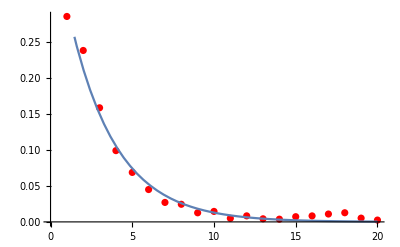

```mathematica
GraphicsGrid[{
ListPlot[#,Filling->Axis,PlotRange->All],
ListPlot[CorrelationFunction[#,{20}],Filling->Axis,PlotRange->All]
}&/@{arrivalintervals,serviceintervals,incrmntintervals,waitingintervals}//Transpose]
```

Effect of utility rate

Results from a queue with poisson arrival (λ=0.1) and exponential service (μ=1.5).

-Graphics-

Results from a queue with poisson arrival (λ=1.0) and exponential service (μ=1.5).

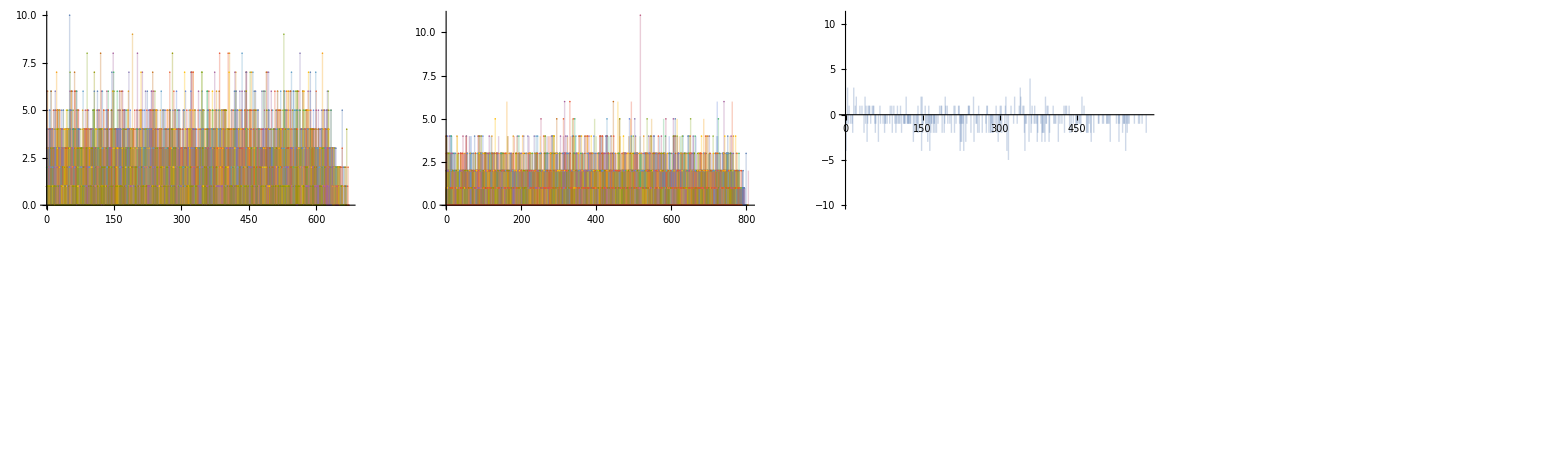

Results from a queue with poisson arrival (λ=1.45) and exponential service (μ=1.5).

-Graphics-

Effect of correlated increments

Results from a queue with poisson arrival (λ=1.0) and exponential service (μ=1.5).

-Graphics-

Results from a queue with auto-correlated arrival (λ≈1.0) and exponential service (μ=1.5).

-Graphics-

Note that waiting times are always strongly correlated; but the correlation of increments do increase that of the waiting times.

Show[{ListPlot[CorrelationFunction[waitingintervals,{20}],Filling→Axis,PlotRange→All,PlotStyle→Red],-Graphics-}]

-Graphics-

## New stuff